# Rania —PS 8 (02.18.2025)

## Sections 20, 21, 22 in EIWL3

## Section 20: Options

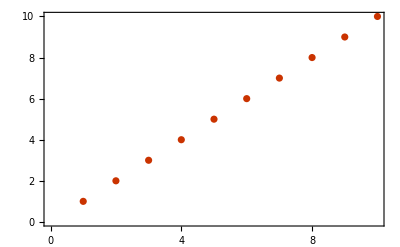

```mathematica
(*20.1 A list plot of Range[10] themed for the web*)
ListPlot[Range[10], PlotTheme->"Web"]
```

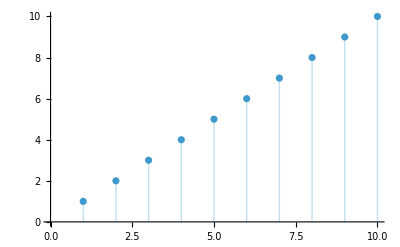

```mathematica
(*20.2 A list plot of Range[10] with filling to the axis*)
ListPlot[Range[10], Filling -> Axis]
```

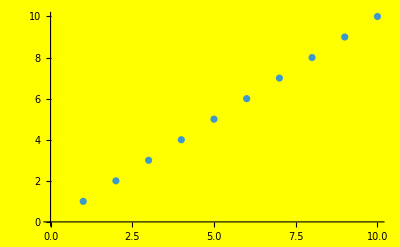

```mathematica
(*20.3 A list plot of Range[10] with a yellow background*)
ListPlot[Range[10], Background->Yellow]
```

```mathematica
(*20.4 Map of the world with Australia highlighted*)
GeoListPlot[Entity["Country","Australia"],GeoRange->All]
```

-Graphics-

```mathematica
(*20.5 Map of the Indian Ocean with Madagascar highlighted.*)
GeoListPlot[Entity["Country","Madagascar"],GeoRange-> Entity["Ocean","IndianOcean"]]
```

-Graphics-

```mathematica
(*20.6 GeoGraphics to create a map of South America showing topography (relief map).*)
GeoGraphics[EntityClass["Country","SouthAmerica"], GeoBackground->"ReliefMap"]
```

-Graphics-

```mathematica
(*20.7 Map of Europe with France, Finland, and Greece highlighted and labeled*)
GeoListPlot[{Entity["Country","France"], Entity["Country","Finland"], Entity["Country","Greece"]}, GeoRange->Entity["GeographicRegion","Europe"], GeoLabels->Automatic]
```

-Graphics-

```mathematica
(*20.8 Positions of universities in the Ivy League, labeling each*)
(*during transfer season?!! really Wolfram....*)
GeoListPlot[EntityClass["University","TheIvyLeague"], GeoLabels->Automatic]
```

-Graphics-

```mathematica
(*20.9 12×12 multiplication table as a grid with white type on a black background*)
Grid[Table[i*j, {i,12}, {j,12}], Frame-> All,ItemStyle-> White, Background->Black]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*20.10 List of 100 disks with random integer image sizes up to 40*)
Table[Graphics[Disk[], ImageSize->n],{n,0,40,.4}]
```

```mathematica
(*20.11 A list of pictures of regular pentagons with image size 30 and aspect ratios from 1 to 10*)
Table[Graphics[RegularPolygon[5], ImageSize->30, AspectRatio-> n] ,{n,1,10,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*20.12 Manipulate that varies the size of a circle between 5 to 500*)
Manipulate[Graphics[Circle[], ImageSize->n], {n,5,500,1}]
```

```mathematica
(*20.13 A framed 10×10 grid of random colors*)
Grid[Table[RandomColor[],10,10]]
```

RGBColor[0.016095347375026714, 0.44403136644757324, 0.6884272243536986] | RGBColor[0.34680343192661, 0.0797831937056539, 0.9486080909164802] | RGBColor[0.07685674877821524, 0.5449590371103663, 0.1591718528460755] | RGBColor[0.31441742665585015, 0.14043304887616292, 0.6205234400780593] | RGBColor[0.1359450040575807, 0.7992114166715272, 0.15751884585730802] | RGBColor[0.8144680966671505, 0.8027639458667961, 0.7128960931595429] | RGBColor[0.8792559771858524, 0.4017531659103646, 0.8294530512409406] | RGBColor[0.9027996837311567, 0.6490627668103022, 0.9574027330696233] | RGBColor[0.2737895473731753, 0.1623217447233094, 0.10585767795979506] | RGBColor[0.7577450329169453, 0.4924931330140825, 0.33513904273675954]
RGBColor[0.6061263244284538, 0.15029572442721317, 0.1133450910265199] | RGBColor[0.14975525701346948, 0.9899100994860666, 0.17751698819160722] | RGBColor[0.0009781372485175854, 0.949296227352741, 0.43746396211781047] | RGBColor[0.078755710789288, 0.04592195793762133, 0.12436906065003428] | RGBColor[0.5674817635754643, 0.11167307833166507, 0.846824934623112] | RGBColor[0.11044655372444168, 0.4426612036766351, 0.430791000389094] | RGBColor[0.8836527846679438, 0.989142716500885, 0.7870083988111574] | RGBColor[0.010619027114050938, 0.18111306372275027, 0.9632038649743595] | RGBColor[0.9597089010769868, 0.499782739647058, 0.32517435463394095] | RGBColor[0.2301894768234698, 0.9542909255139378, 0.14362439660088788]
RGBColor[0.8145495417216406, 0.7080750145909613, 0.550194135402136] | RGBColor[0.0772059795665927, 0.5216383061701106, 0.5578018447191802] | RGBColor[0.3153947262318133, 0.8710346221673821, 0.1713610645596222] | RGBColor[0.2118688654013039, 0.10141129259546489, 0.9190273264179545] | RGBColor[0.481931770086232, 0.23449168217163052, 0.011680482242845125] | RGBColor[0.436009206115044, 0.08371141041902153, 0.06311425954235172] | RGBColor[0.3771444777965729, 0.30902134747213594, 0.5055395594559913] | RGBColor[0.3765098140530594, 0.6171997407175969, 0.8512161696096319] | RGBColor[0.4309870557032156, 0.05042050508767937, 0.8989934218039086] | RGBColor[0.5512765710307443, 0.6200009068437153, 0.17667045794355318]
RGBColor[0.274927719376836, 0.5777134194177114, 0.5105925845335655] | RGBColor[0.020489170601724283, 0.2601758771480287, 0.5928881154073471] | RGBColor[0.0492927379706507, 0.8619481379844982, 0.7201719824590487] | RGBColor[0.8651821633429084, 0.21874210007714057, 0.17909774292076164] | RGBColor[0.654034810113679, 0.5197613862132646, 0.6647968790205747] | RGBColor[0.17520969884091486, 0.16529590828665208, 0.12701963322635912] | RGBColor[0.257410924663243, 0.1636981687480017, 0.8832589957564727] | RGBColor[0.8732173876804807, 0.27779754167590265, 0.16781648948149241] | RGBColor[0.2552223487928291, 0.672682625521484, 0.45366917551007724] | RGBColor[0.22452412863771642, 0.4898590019689515, 0.6990197111437648]
RGBColor[0.7204805915307804, 0.21521542017612205, 0.9699272402996744] | RGBColor[0.1365258070768034, 0.38520259260841394, 0.8497527344674951] | RGBColor[0.43982981582180813, 0.6138208517849157, 0.15102857792592528] | RGBColor[0.22002411011199752, 0.7702689966605096, 0.47702049615976794] | RGBColor[0.23276269931219296, 0.56098660204901, 0.7499665888748279] | RGBColor[0.7795882656326827, 0.9767032737616284, 0.5197369405901453] | RGBColor[0.018087916567057327, 0.8071430314504426, 0.22812385650958533] | RGBColor[0.29355466550623155, 0.623670523273496, 0.7537697720046932] | RGBColor[0.1944649627872732, 0.5181061940059648, 0.9963418562099728] | RGBColor[0.7117617274014183, 0.21284785744023882, 0.5664824383679399]
RGBColor[0.276179099589857, 0.4150736977711966, 0.666830701350837] | RGBColor[0.6295469705653394, 0.16529567804437084, 0.12717648998689302] | RGBColor[0.26663987728382366, 0.46947205848722207, 0.3806711418259443] | RGBColor[0.6345723525842244, 0.11759065871909113, 0.3857490426996968] | RGBColor[0.2768374171824095, 0.12312791258214961, 0.01672743112578834] | RGBColor[0.20515014692785916, 0.06239686246848786, 0.31799944729673935] | RGBColor[0.4886639360906819, 0.11524995586824938, 0.7289900259081123] | RGBColor[0.9542065478975921, 0.16141461898682619, 0.4748035245214226] | RGBColor[0.5141025135817912, 0.7244716966909135, 0.24423775711884654] | RGBColor[0.9772726827398075, 0.23139970944209942, 0.5352078494092636]
RGBColor[0.8740924933669643, 0.9397996165236682, 0.7937769348810844] | RGBColor[0.17248303819043387, 0.5128898607729253, 0.5483125255796966] | RGBColor[0.5141576573768611, 0.48702665919678756, 0.8104013550082674] | RGBColor[0.561515082945399, 0.06046977475136339, 0.8467428678994164] | RGBColor[0.5481828558975996, 0.902826922293746, 0.2604935959485233] | RGBColor[0.08982135161424387, 0.445138424599002, 0.9137140371240382] | RGBColor[0.023378379959036133, 0.6984872516532925, 0.5705969389857617] | RGBColor[0.09936668930753356, 0.7070680103695148, 0.2122314252895372] | RGBColor[0.7622355548466311, 0.8377898745730188, 0.1079488196365308] | RGBColor[0.4112675681323108, 0.3801863830368952, 0.9495212116637084]
RGBColor[0.053220644772797865, 0.5753478910688337, 0.760765950300051] | RGBColor[0.5492758813065983, 0.3634505558803649, 0.806900596602514] | RGBColor[0.7430244979571279, 0.5170822275226781, 0.46931122056420094] | RGBColor[0.742747260646581, 0.7579480089767299, 0.003534774599183166] | RGBColor[0.1445835306292904, 0.74586898878595, 0.5699223606033934] | RGBColor[0.11266265417366284, 0.36644990272036204, 0.7675495976682751] | RGBColor[0.9667927409816635, 0.7965299951217584, 0.07882820240702637] | RGBColor[0.6639623137115218, 0.5379903100775465, 0.7533725536244114] | RGBColor[0.47123993025235356, 0.7061382884422278, 0.01872956531288472] | RGBColor[0.13357535648324625, 0.13585320836089743, 0.7281536161160593]
RGBColor[0.7805631453687589, 0.13980327665153625, 0.015587629633126765] | RGBColor[0.1614623009101337, 0.8205398317528465, 0.9391654135161931] | RGBColor[0.19292807841155724, 0.25349713938521323, 0.6755570393704702] | RGBColor[0.18141021508852728, 0.2974837343965413, 0.07095347669155028] | RGBColor[0.042296001541349604, 0.820519544094475, 0.8715088116459084] | RGBColor[0.1655179410141372, 0.27706507429508487, 0.4651459198364558] | RGBColor[0.17767872633899584, 0.824449287777727, 0.6913924467357968] | RGBColor[0.2215215278277718, 0.35197834109025994, 0.24038671281363366] | RGBColor[0.0021197369795113996, 0.6214007967494528, 0.651018132500796] | RGBColor[0.8288844082282618, 0.07428034071178313, 0.6034681487760223]
RGBColor[0.578776242406829, 0.2750963978117704, 0.04167876232436063] | RGBColor[0.4484097315882216, 0.010844235973048733, 0.6439166315398157] | RGBColor[0.33577316919778255, 0.20784085425770082, 0.36392522779123837] | RGBColor[0.648012592521191, 0.8549385638844038, 0.4583672755296666] | RGBColor[0.8296517548510738, 0.6814752906009907, 0.7480333572550002] | RGBColor[0.16678712788965244, 0.2904608803746087, 0.113932061275281] | RGBColor[0.8412788775491942, 0.2536033190322666, 0.8583344964521509] | RGBColor[0.7489832210988474, 0.9381286749657087, 0.3959535111794006] | RGBColor[0.6796356461540112, 0.27941453588235365, 0.15572682811641547] | RGBColor[0.5579330868203942, 0.6556964643066447, 0.8667009366131808]

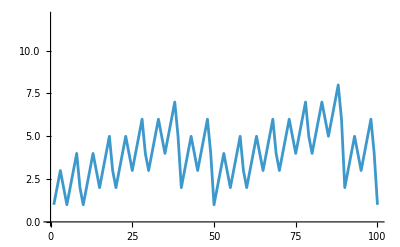

```mathematica
(*20.14 A line plot of the lengths of Roman numerals up to 100,with a plot range that would be sufficient for all numerals up to 1000*)
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}],PlotRange->{0,12}]
```

## Section 21: Graphs and Networks

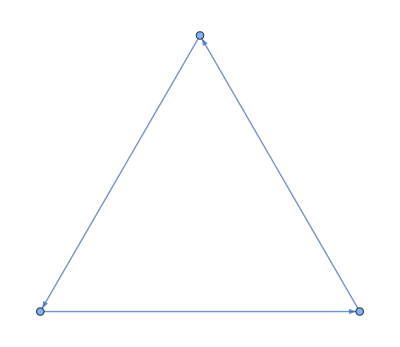

```mathematica
(*21.1 Graph of a loop of 3 nodes*)
Graph[{1->2,2->3, 3->1}]
```

```mathematica
(*21.2 Agraph with 4 nodes in which every node is connected*)
Graph[Flatten[Table[i->j,{i,4},{j,4}]]]
```

-Graphics-

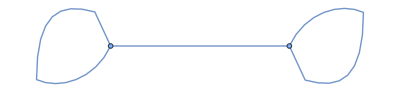
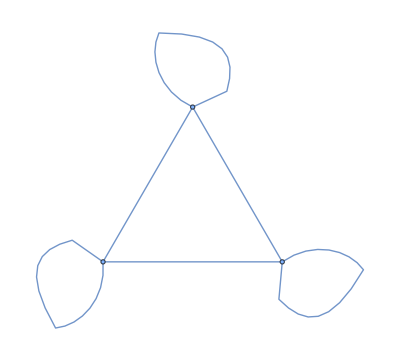
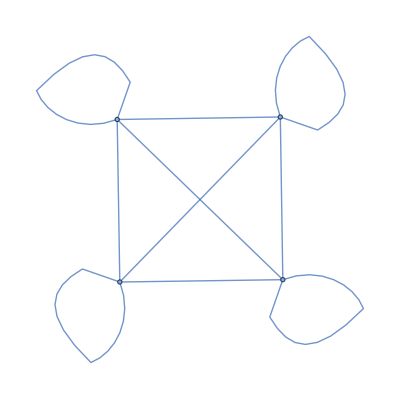
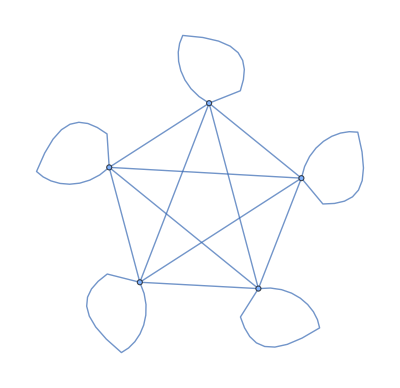
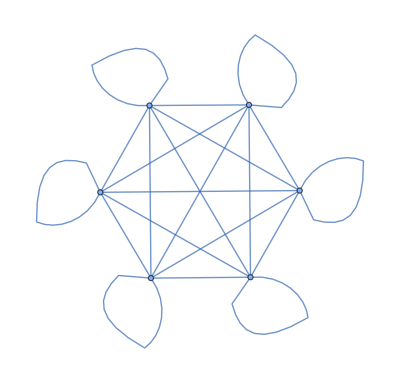
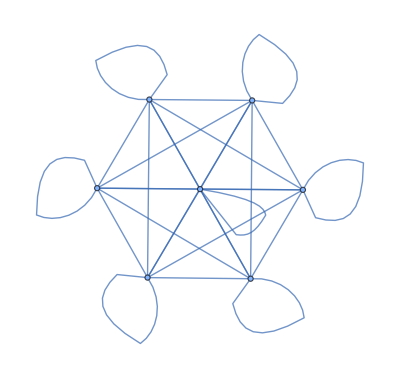
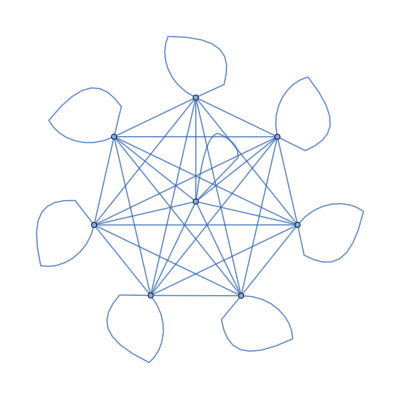
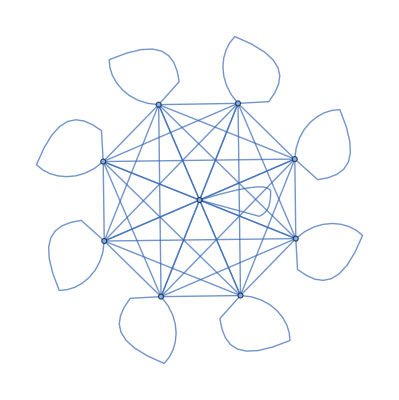

```mathematica
(*21.3 Table of undirected graphs with between 2 and 10 nodes in which every node is connected*)
Table[UndirectedGraph[Flatten[Table[i->j,{i,n},{j,n}]]],{n,2,10,1}]
```

```mathematica
(*21.4 Use Table and Flatten to get {1,2,1,2,1,2}*)
Flatten[Table[Range[2],3]]
```

{1,2,1,2,1,2}

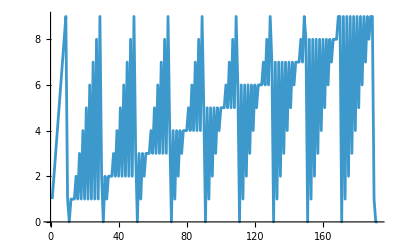

```mathematica
(*21.5 A line plot of the result of concatenating all digits of all integers from 1 to 100 (i.e....,8,9,1,0,1,1,1,2,...)*)
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

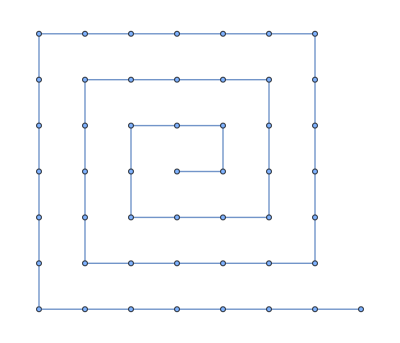

```mathematica
(* 21.6 Make a graph with 50 nodes,in which node i connects to node i+1 *)UndirectedGraph[Table[i->i+1, {i,49}]]
```

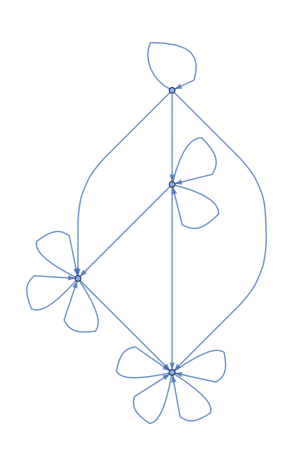

```mathematica
(*21.7 Graph with 4 nodes,in which each connection connects i to Max[i,j]*)Graph[Flatten[Table[i-> Max[i,j], {i,4},{j,4}]]]
```

```mathematica
(*21.8 Graph in which each connection connects i to j-i,where i and j both range from 1 to 5.*)
Graph[Flatten[Table[i->j-i,{i,5},{j,5}]]]
```

-Graphics-

```mathematica
(*21.9 Generate a graph with 100 nodes,each with a connection going to one randomly chosen node.*)
Graph[Table[RandomInteger[99]->RandomInteger[99],100]]
```

-Graphics-

```mathematica
(*21.10 A graph with 100 nodes,each connecting to two randomly chosen nodes.*)
Graph[Flatten[Table[{n->RandomInteger[99],n->RandomInteger[99]},{n,0,99}]]]
```

-Graphics-

```mathematica
(*21.11 For the graph {1->2,2->3,3->4,4->1,3->1,2->2},make a grid giving the shortest paths between every pair of nodes,with the start node as row and end node as column.*)
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],n,j],{n,4},{j,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Section 22: Machine Learning

```mathematica
(*22.1 Identify what language the word “ajatella” comes from*)
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
(*22.2 Apply ImageIdentify to an image of a tiger,getting the image using ctrl+=*)
ImageIdentify[Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]]]
```

tiger

```mathematica
(*22.3 Make a table of image identifications for an image of a tiger,blurred by an amount from 1 to 5*)
Table[ImageIdentify[Blur[Entity["TaxonomicSpecies","PantheraTigris::63rj9"][EntityProperty["TaxonomicSpecies","Image"]], n]],{n,1,5}]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
(*22.4 Classify the sentiment of “I’m so happy to be here”.*)
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
(*22.5 Find the 10 words in WordList[] that are nearest to “happy” *)
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
(*22.6 20 random numbers up to 1000 and find which 3 are nearest to 100.*)
Nearest[Table[RandomInteger[1000],20],100,3]
```

{64,62,44}

```mathematica
(*22.7 A list of 10 random colors,and which 5 are closest to Red*)
Nearest[Table[RandomColor[],10],Red,5]
```

{RGBColor[0.6404118798938312, 0.6525689413125237, 0.18242493578804608],RGBColor[0.775437918330258, 0.7134572912098425, 0.5955091437466222],RGBColor[0.6978658661955872, 0.5536710541034338, 0.6702321565664635],RGBColor[0.8789978738772481, 0.7546338293754904, 0.8433667657979125],RGBColor[0.6716119482616081, 0.7547062487006293, 0.5671908783117019]}

```mathematica
(*22.8 Of the first 100 squares,find the one nearest to 2000*)
Nearest[Table[x^2,{x,1,100}],2000]
```

{2025}

```mathematica
(*22.9 Find the 3 European flags nearest to the flag of Brazil.*)
Nearest[EntityClass["Country","Europe"][EntityProperty["Country","Flag"]], Entity["Country","Brazil"][EntityProperty["Country","Flag"]],3]
```

{-Graphics-,-Graphics-,-Graphics-}

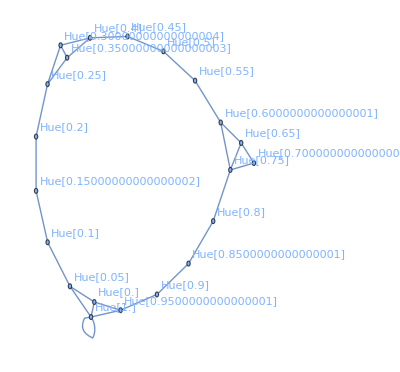

```mathematica
(*22.10 A graph of the 2 nearest neighbors of each color in Table[Hue[h],{h,0,1,.05}]*)
colorList = Table[Hue[h],{h,0,1,.05}];
NearestNeighborGraph[colorList,2,VertexLabels->All]
```

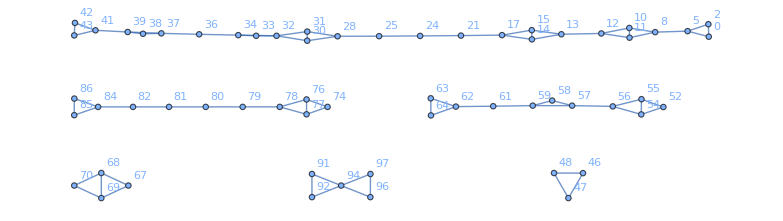

```mathematica
(*22.11 A list of 100 random numbers from 0 to 100,and make a graph of the 2 nearest neighbors of each one*)
randomNumto100 = Table[RandomInteger[100],100];
NearestNeighborGraph[randomNumto100, 2, VertexLabels->All]
```


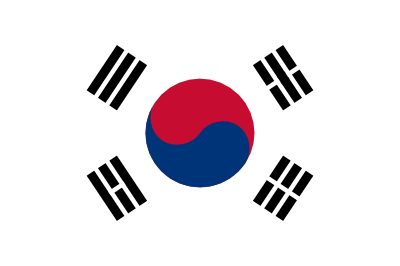
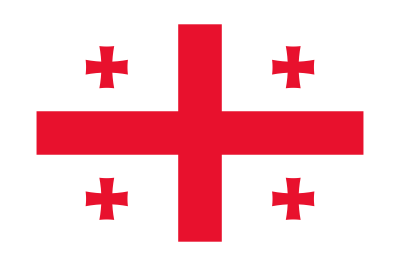
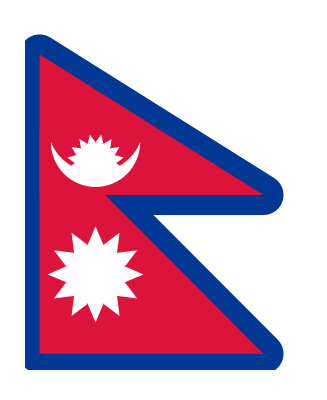
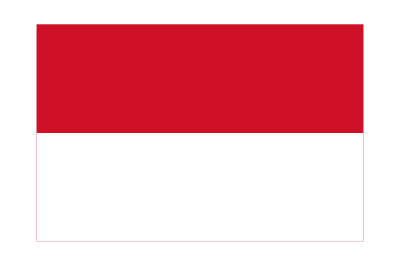
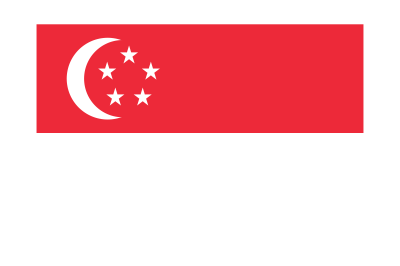
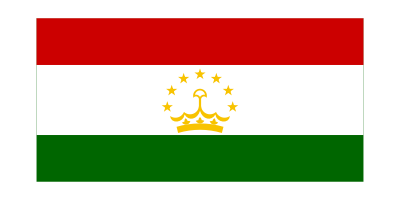
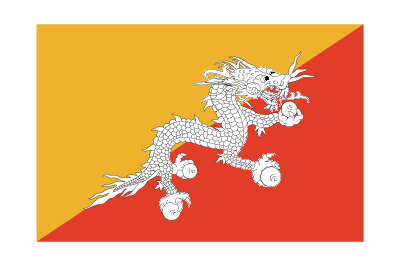
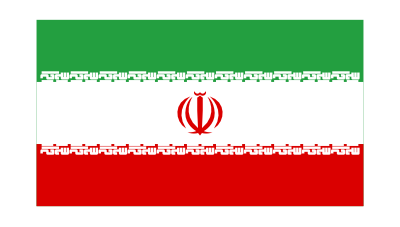

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
(*22.12 Collect the flags of Asia into clusters of similar flags*)
FindClusters[EntityClass["Country","Asia"][EntityProperty["Country","Flag"]]]
```

```mathematica
(*22.13 Make raster images of the letters of the alphabet at size 20,then make a graph of the 2 nearest neighbors of each one*)
NearestNeighborGraph[Table[Rasterize[FromLetterNumber[n],RasterSize->20],{n,26}],2,VertexLabels->Automatic]
```

-Graphics-

```mathematica
(*22.14 Generate a table of the results from applying TextRecognize to the EdgeDetect of the word “programming” rasterized at sizes between 10 and 20*)
Table[TextRecognize[EdgeDetect[Rasterize["programming",RasterSize->n]]],{n,10,20,1}]
Table[TextRecognize[EdgeDetect[Rasterize[Style["programming",n]]]],{n,10,20,1}]

(*confusing..I don't understand the excercise nor can I get the desired output, even when trying a Rasterize from 1 -> 100. Here are my two way of interperting the problem*)
```

{,,,,,,,,,,}

{orogramming,programming,programming,programming,programming,programming,programming,programming,programming,programming,programming}

```mathematica
(*22.15 Make a dendrogram for images of the first 10 letters of the alphabet.*)
Dendrogram[Table[Rasterize[FromLetterNumber[n]],{n,10}]]
```

-Graphics-

```mathematica
(*22.16 Make a feature space plot for the uppercase letters of the alphabet.*)
FeatureSpacePlot[Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]]
```

-Graphics-